## SEU.AAA.25.05 Modelling by Numbers

## exercises

Stephen Wolfram: An Elementary Introduction to the Wolfram Language. Chapters 30 - 32 - lists and patterns

## model as code - about the HARMONIC domain

-Graphics-

### remember the law of large numbers

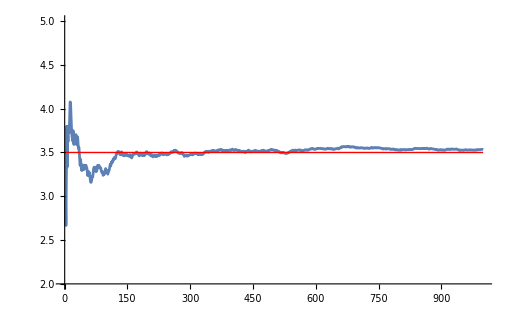

```mathematica
n = 1000;
Show[
ListLinePlot[
Accumulate@RandomInteger[{1,6}, n]/Range@n, 
PlotRange->{{0,n}, {2.,5}}, 
ImageSize->512],
Graphics[
{Red, Line[{{0,3.5},{n,3.5}}]}
]
]
```

### 1D

#### in 'time domain', what we called the DAY or SPACE

```mathematica
f = 3;
Show[
 Plot[Sin[x 2 f π], {x, 0, 1},
 Axes->{True, False}
],
 Graphics[{
   Red, Thickness@.005, Line[{{0, 0}, {1, 0}}],
   PointSize@.02, Point[{# , 0}] & /@ Range[0, 1, 1/f/2][[2;;-2]],
   Line[{{0,-1/2},{0,1/2}}],Line[{{1,-1/2},{1,1/2}}]
   }]
 ]
```

blue: the circular line in TIME [the production],
red: the linear circle of SPACE [the article]

#### in ‘frequency domain’, what we called the NIGHT or TIME

```mathematica
f = 3;
data =N@ Table[Sin[x 2 f π], {x, 0, 1,1/200}]
```

```mathematica
ListPlot@data
```

the production

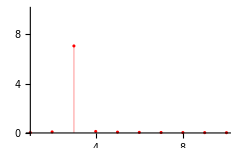

```mathematica
dF =Rest@Fourier@data;
ListPlot[Abs@dF, PlotRange -> {{1, 10}, {0, 10}}, Filling -> Axis, 
 PlotStyle -> Red, ImageSize -> 240]
```

#### you can produce any FORM by an overlay of FREQUENCIES

start with a list of points of a FORM

```mathematica
data =N@ Table[x, {x, 0, 1,1/50}];
ListPlot@data
```

any form in time-domain is produced by FREQUENCIES

```mathematica
dF =Rest@Fourier@data;
ListPlot[Abs@dF, PlotRange -> {{0, 10}, {0, 3}}, Filling -> Axis, 
 PlotStyle -> Red, ImageSize -> 240]
```

they are read as parameters to sinus functions

```mathematica
MapIndexed[#1 Sin[x 2 First@#2 π]&,Abs[dF][[1;;12]]]
```

{1.16006 Sin[2 π x],0.581132 Sin[4 π x],0.38865 Sin[6 π x],0.292785 Sin[8 π x],0.235572 Sin[10 π x],0.197691 Sin[12 π x],0.170864 Sin[14 π x],0.150952 Sin[16 π x],0.135657 Sin[18 π x],0.123602 Sin[20 π x],0.113912 Sin[22 π x],0.106004 Sin[24 π x]}

these  sinus functions can be rendered

```mathematica
n = 12;
Plot[MapIndexed[-#1 Sin[x 2 First@#2 π]&,Abs[dF][[1;;n]]], {x, 0, 1},
 Axes->{True, False}
]
```

or  summed  up to adapt the points of the given form

```mathematica
n = 12;
Plot[Total@MapIndexed[-#1 Sin[x 2 First@#2 π]&,Abs[dF][[1;;n]]], {x, 0, 1},
 Axes->{True, False}
]
```

### 2D

a plot of 2-dimensional waves

```mathematica
f = 3;
DensityPlot[Sin[f 2 π x] Cos[f 2 π y], {x, 0, 1}, {y, 0, 1}, 
 ColorFunction -> GrayLevel]
```

instead of points on a line (1D) you have grid lines on a plane (2D)

```mathematica
Show[
 ContourPlot[Sin[2f π x] Cos[2 f π y], {x, 0, 1}, {y, 0, 1}, 
  ColorFunction -> GrayLevel],
 Graphics[{
   Red, Line[{{0, # }, {1, # }}] & /@ Range[1/f/4, 1, 1/f/2],
   Line[{{#, 0 }, { #, 1 }}] & /@ Range[0, 1, 1/f/2]
   }]
 ]
```

gray : the  circular lines  in  TIME [the  production],
red : the  linear  circle  of  SPACE [the  articulation]

all images are frequencies in synchronicity - a ‘chord’
they are renderings of a sound

#### this is how it works

the time domain

```mathematica
b = -Graphics-;
{h, w} = ImageDimensions@b
```

{240,182}

the freq domain

```mathematica
fou = Fourier[ImageData[ColorSeparate[b][[1]]]];
```

```mathematica
ListPointPlot3D[Abs[fou][[2 ;; 36, 2 ;; 36]], 
 PlotStyle -> Directive[Red, PointSize[.01]], Filling -> Axis, 
 PlotRange -> {{0, 36}, {0, 36}, {-1, 10}}, Boxed -> False, 
 Axes -> False, ImageSize -> 192]
```

take a high-pass filter and render the frequencies back to time domain

```mathematica
nw =24;
nh = Round[h nw/w];
fou = Fourier[ImageData[b]];
Table[fou[[i, j]] = {0, 0, 0}, {i, nw, w - nw}, {j, 1, h}];
Table[fou[[i, j]] = {0, 0, 0}, {i, 1, w}, {j, nh, h - nh}];

img = Image@Re@InverseFourier[fou]
imgRGB = ColorSeparate@img;
imgRGB[[1]]
imgRGB[[2]]
imgRGB[[3]]
```

### 3D

```mathematica
ContourPlot3D[ 
 Cos[x] Sin[y] + Cos[y] Sin[z] + Cos[z] Sin[x] == 0, {x, -2 π, 
  2 π}, {y, -2 π, 2 π}, {z, -2 π, 2 π}, 
 ContourStyle -> 
  Directive[FaceForm[Orange, Red], Specularity[White, 30]], 
 Mesh -> None]
```

## model as code - starter

also see youtube  lecture

#### the numbers

```mathematica
d1 = Range@12;
d2 = Range@6;
coords = Tuples[{d1, d2}]
```

#### the rendering as GRAPHICS

```mathematica
G1=Graphics[{
{Blue,Point@#}&/@coords},
ImageSize->480,
PlotRange->{{0,13},{0,7}}
]
```

#### selecting

```mathematica
G1[[1]]
```

```mathematica
Cases[G1, Point[{3, _}], All]
```

```mathematica
Graphics@Cases[G1,Point[{x_,y_}]/;3<=x<=4||y==3,All]
```

#### changing

```mathematica
G2 = Replace[
  G1,
{___, Point[{x_, y_}]} /; 2 < x < 8 && 2 < y < 5 
:> {Red,PointSize@.03, Point[{x, y}]},
 All]
```

#### subgraphic

```mathematica
G3=DeleteCases[G2,
{___,Point[{x_,y_}],___}/;x>5,
All]
```

#### counting

```mathematica
Length@Cases[G3,{___,Red,___,Point[_],___},All]
```

#### translating to 3D

```mathematica
g3 = Replace[G2[[1]], {
   {Red, ___, Point[{x_, y_}]} :> {Red, Sphere[{x, y, 0}, .2]},
   {Blue, ___, Point[{x_, y_}]} :> {EdgeForm[], Gray,Cuboid[{x, y, 0} - .1, {x, y, 0} + .1 ]}
   }, All]
```

```mathematica
G3 = Graphics3D[
  g3, 
  Boxed -> False,
  Lighting -> "Neutral"
  ]
```